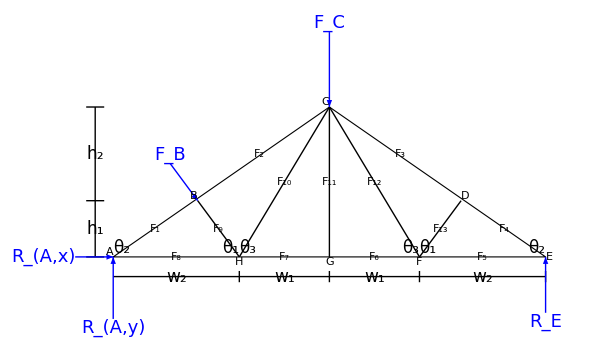

```mathematica
Module[{FB,FC,w1,w2,h1,h2,L,H,θ1,z1,θ2,θ3,reactions,RAx,RAy,RE,scale},
FB=2;FC=5;
w1=5;w2=7;h1=3;h2=5;L=2*(w1+w2);H=h1+h2;

θ1=ArcTan[h1/(0.33*w2)];z1=√(h1^2+(0.67*w2)^2);θ2=ArcTan[h1/(0.67*w2)];θ3=ArcTan[(h1+h2)/w1];

reactions=Quiet@Solve[{
rax+FB*Cos[θ1]==0,
z1*FB-2*(w1+w2)*re+(w1+w2)*FC==0,
ray-FB*Sin[θ1]+re-FC==0
},{rax,ray,re}][[1]];
RAx=rax/.reactions;RAy=ray/.reactions;RE=re/.reactions;

scale[F_]:=1.5+5*Rescale[Abs@F,{0,10}];

Graphics[{Thick,
{Thick,Line[{{w2,0},{0.67*w2,h1}}],Line[{{w2,0},{w1+w2,H}}],Line[{{2*w1+w2,0},{L-0.67*w2,h1}}],Line[{{2*w1+w2,0},{w1+w2,H}}],Line[{{w1+w2,0},{w1+w2,H}}],
EdgeForm@Thick,FaceForm@None,Polygon[{{0,0},{L,0},{w1+w2,H}}]},

{Thin,Line[{{0,-0.35*h1},{L,-0.35*h1}}],Line[{{#,-0.25*h1},{#,-0.45*h1}}]&/@{w2,w2+w1,w2+2*w1,L},
Text[Style[Subscript[Style["w",Italic],#1],17,Background->White],{#2,-0.35*h1}]&@@@{{2,0.5*w2},{1,w2+0.5*w1},{1,w2+1.5*w1},{2,1.5*w2+2*w1}},

Line[{{-0.2*w1,0},{-0.2*w1,H}}],Line[{{-0.3*w1,#},{-0.1*w1,#}}]&/@{0,h1,H},
Text[Style[Subscript[Style["h",Italic],#1],17,Background->White],{-0.2*w1,#2}]&@@@{{1,0.5*h1},{2,h1+0.5*h2}}},

Text[Style[Subscript[Style["θ",Italic],#1],17],{#2,0},1.2*#3]&@@@{{1,w2,{2,-1}},{1,2*w1+w2,{-2,-1}},{2,0,{-2.5,-0.7}},{2,L,{2.5,-0.7}},{3,w2,{-2,-1}},{3,2*w1+w2,{2,-1}}},

{Thick,Blue,
Arrow[{{0.67*w2-scale[FB]*Cos[θ1],h1+scale[FB]*Sin[θ1]},{0.67*w2,h1}}],
Arrow[{{w1+w2,h1+h2+scale[FC]},{w1+w2,h1+h2}}],
Text[Style[Subscript[Style["F",Italic],#2],18,Blue],#3,#4]&@@@{{FB,"B",{0.67*w2-scale[FB]*Cos[θ1],h1+scale[FB]*Sin[θ1]},{0.,-1}},{FC,"C",{w1+w2,h1+h2+scale[FC]},{0,-1.5}}},
Arrow[{{0,-scale[RAy]},{0,0}}],Arrow[{{-scale[RAx],0},{0,0}}],
Text[Style[Subscript[Style["R",Italic],Row@{"A,",Style[#2,Italic]}],18],#3,#4]&@@@{{RAx,"x",{-scale[RAx],0},{1.1,0}},{RAy,"y",{0,-scale[RAy]},{0,1.5}}},
Arrow[{{2*(w1+w2),-scale[RE]},{2*(w1+w2),0}}],
Text[Style[Subscript[Style["R",Italic],"E"],18],{2*(w1+w2),-scale[RE]},{0,1.5}]},

Text[Framed[Style[Subscript[Style["F",Italic],#1],18],Background->White,FrameStyle->None,FrameMargins->Tiny],#2]&@@@{{1,{0.67*w2,h1}/2},{8,{w2/2,0}},{2,{0.8*w2+w1/2,h1+h2/2}},{9,{0.67*w2+0.33*w2/2,h1/2}},{10,{w2+w1/2,(h1+h2)/2}},{11,{w1+w2,(h1+h2)/2}},{12,{1.5*w1+w2,(h1+h2)/2}},{3,{2*w1+0.85*w2,h1+h2/2}},{4,{2*w1+1.67*w2,h1/2}},{13,{2*w1+w2+0.33*w2/2,h1/2}},{5,{2*w1+1.5*w2,0}},{6,{1.5*w1+w2,0}},{7,{w1/2+w2,0}}},

Text[Framed[Style[Row@{" ",#1," "},17],RoundingRadius->15,FrameMargins->Small],#2,#3]&@@@{{"A",{0,0},{0.5,-1}},{"B",{0.67*w2,h1},{2,-0.5}},{"C",{w1+w2,H},{1.5,-1}},{"D",{2*w1+1.33*w2,h1},{-1,-1}},{"E",{L,0},{-1,0}},{"F",{2*w1+w2,0},{0,1}},{"G",{w1+w2,0},{0,1}},{"H",{w2,0},{0,1}}}
},ImageSize->600]
]
```

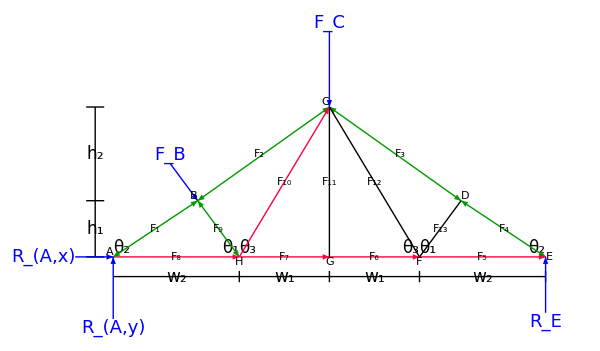

```mathematica
Module[{FB,FC,w1,w2,h1,h2,L,H,θ1,z1,θ2,θ3,reactions,RAx,RAy,RE,colC,colT,scale},
FB=2;FC=5;
w1=5;w2=7;h1=3;h2=5;L=2*(w1+w2);H=h1+h2;

θ1=ArcTan[h1/(0.33*w2)];z1=√(h1^2+(0.67*w2)^2);θ2=ArcTan[h1/(0.67*w2)];θ3=ArcTan[(h1+h2)/w1];

reactions=Quiet@Solve[{
rax+FB*Cos[θ1]==0,
z1*FB-2*(w1+w2)*re+(w1+w2)*FC==0,
ray-FB*Sin[θ1]+re-FC==0
},{rax,ray,re}][[1]];
RAx=rax/.reactions;RAy=ray/.reactions;RE=re/.reactions;

colC=RGBColor[0,0.6,0];colT=RGBColor[1,0,0.25];
scale[F_]:=1.5+5*Rescale[Abs@F,{0,10}];

Graphics[{Thick,
{Thin,Line[{{0,-0.35*h1},{L,-0.35*h1}}],Line[{{#,-0.25*h1},{#,-0.45*h1}}]&/@{w2,w2+w1,w2+2*w1,L},
Text[Style[Subscript[Style["w",Italic],#1],17,Background->White],{#2,-0.35*h1}]&@@@{{2,0.5*w2},{1,w2+0.5*w1},{1,w2+1.5*w1},{2,1.5*w2+2*w1}},

Line[{{-0.2*w1,0},{-0.2*w1,H}}],Line[{{-0.3*w1,#},{-0.1*w1,#}}]&/@{0,h1,H},
Text[Style[Subscript[Style["h",Italic],#1],17,Background->White],{-0.2*w1,#2}]&@@@{{1,0.5*h1},{2,h1+0.5*h2}}},

Text[Style[Subscript[Style["θ",Italic],#1],17],{#2,0},1.2*#3]&@@@{{1,w2,{2,-1}},{1,2*w1+w2,{-2,-1}},{2,0,{-2.5,-0.7}},{2,L,{2.5,-0.7}},{3,w2,{-2,-1}},{3,2*w1+w2,{2,-1}}},

{Blue,
Arrow[{{0.67*w2-scale[FB]*Cos[θ1],h1+scale[FB]*Sin[θ1]},{0.67*w2,h1}}],
Arrow[{{w1+w2,h1+h2+scale[FC]},{w1+w2,h1+h2}}],
Text[Style[Subscript[Style["F",Italic],#2],18,Blue],#3,#4]&@@@{{FB,"B",{0.67*w2-scale[FB]*Cos[θ1],h1+scale[FB]*Sin[θ1]},{0.,-1}},{FC,"C",{w1+w2,h1+h2+scale[FC]},{0,-1.5}}},
Arrow[{{0,-scale[RAy]},{0,0}}],Arrow[{{-scale[RAx],0},{0,0}}],
Text[Style[Subscript[Style["R",Italic],Row@{"A,",Style[#2,Italic]}],18],#3,#4]&@@@{{RAx,"x",{-scale[RAx],0},{1.1,0}},{RAy,"y",{0,-scale[RAy]},{0,1.5}}},
Arrow[{{2*(w1+w2),-scale[RE]},{2*(w1+w2),0}}],
Text[Style[Subscript[Style["R",Italic],"E"],18],{2*(w1+w2),-scale[RE]},{0,1.5}]},

{colC,Arrowheads@{-0.045,0.045},Arrow[{{0,0},{0.67*w2,h1}}],Arrow[{{0.67*w2,h1},{w1+w2,H}}],Arrow[{{0.67*w2,h1},{w2,0}}],Arrow[{{w1+w2,H},{2*w1+1.33*w2,h1}}],Arrow[{{2*w1+1.33*w2,h1},{L,0}}]},

{colT,Arrowheads@{{0.045,0.325},{-0.045,0.675}},Arrow[{{0,0},{w2,0}}],Arrow[{{w2,0},{w1+w2,0}}],Arrow[{{w1+w2,0},{2*w1+w2,0}}],Arrow[{{2*w1+w2,0},{L,0}}],Arrow[{{w2,0},{w1+w2,H}}]},

Line[{{w1+w2,0},{w1+w2,H}}],Line[{{w1+w2,H},{2*w1+w2,0}}],Line[{{2*w1+w2,0},{2*w1+1.33*w2,h1}}],

Text[Framed[Style[Subscript[Style["F",Italic],#1],18],Background->White,FrameStyle->None,FrameMargins->Tiny],#2]&@@@{{1,{0.67*w2,h1}/2},{8,{w2/2,0}},{2,{0.8*w2+w1/2,h1+h2/2}},{9,{0.67*w2+0.33*w2/2,h1/2}},{10,{w2+w1/2,(h1+h2)/2}},{11,{w1+w2,(h1+h2)/2}},{12,{1.5*w1+w2,(h1+h2)/2}},{3,{2*w1+0.85*w2,h1+h2/2}},{4,{2*w1+1.67*w2,h1/2}},{13,{2*w1+w2+0.33*w2/2,h1/2}},{5,{2*w1+1.5*w2,0}},{6,{1.5*w1+w2,0}},{7,{w1/2+w2,0}}},

Text[Framed[Style[Row@{" ",#1," "},17],RoundingRadius->15,FrameMargins->Small],#2,#3]&@@@{{"A",{0,0},{0.5,-1}},{"B",{0.67*w2,h1},{2,-0.5}},{"C",{w1+w2,H},{1.5,-1}},{"D",{2*w1+1.33*w2,h1},{-1,-1}},{"E",{L,0},{-1,0}},{"F",{2*w1+w2,0},{0,1}},{"G",{w1+w2,0},{0,1}},{"H",{w2,0},{0,1}}}
},ImageSize->600]
]
```